## Black Holes, Problem Set 10 for Thursday, Nov. 7

## Reading from Exploring Black Holes

Study Chapter 2 through p. 2-20. This is a long chapter. We’ll save the rest for next time.

## Presentation

Sasha and Eden see Problem 2 below.

## For Problem Set 9

## Problem 1 — Practice with Parametrized Paths

Here is a very cool path, to be considered from ϕ=0 to ϕ=π:       r(ϕ)=(a(1-f^2))/(1-fcosϕ).    In this formula, a and f are just numbers. Let us graph this function with a=5 and f=4/5, in which case it simplifies to:

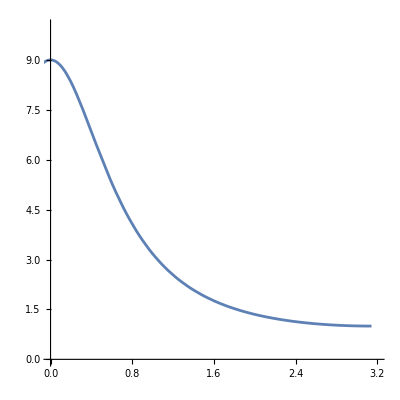

```mathematica
r[ϕ_]:=9/(5-4Cos[ϕ]);
Plot[r[ϕ], {ϕ, -Pi,Pi}, PlotRange->{{0, 3.2},{0, 10}}, AspectRatio->1]
```

It is of course a continuous function, but we are going to manually make some estimates regarding this function and it is easiest to do that if we make the estimates on a discrete and modest number of segments — let’s make that 6 segments numbered from 0 to 5, and there will be 7 points.

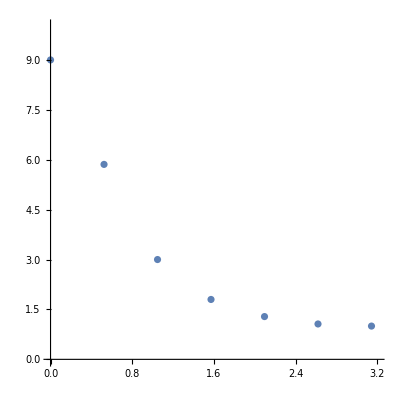

```mathematica
ListPlot[Table[{ϕ,r[ϕ]}, {ϕ, 0, Pi, Pi/6}], PlotRange->{{0, 3.2},{0, 10}}, AspectRatio->1]
```

#### (a) Tabulate Δϕ for each of the six segments

That is so easy, it shouldn’t even be a step! The points are π/6 apart on the horizontal axis so all the Δϕ values are the same. Also, π/6 is about 0.52. Heck, I’ll just have Mathematica make that table for you:

```mathematica
TableForm[Table[{0.52}, {i, 0, 5}],TableHeadings->{Range[0, 5], {"Δφ"}}]
```

| Δφ
0 | 0.52
1 | 0.52
2 | 0.52
3 | 0.52
4 | 0.52
5 | 0.52

### (b) Tabulate r and Δr for each of the eight segments

Now you have some estimates to make and a table to fill in. What should you use for r? Let’s use the average of the r- value of the left and right endpoints of each segment. And for Δr? Just use the difference (which is negative, because this is a decreasing function of ϕ, but in part (c) you will see that only the square of the difference matters). Do your estimates to 1-decimal place accuracy. It won’t matter much if you round odd decimals up or down.

```mathematica
TableForm[Table[{Round[r[i Pi / 6],0.1], Round[r[(i+1)Pi / 6],0.1], Round[(r[i*Pi /6] + r[(i+1)Pi / 6])/2,0.1], Round[r[i*Pi /6] - r[(i+1)Pi / 6],0.1]}, {i, 0, 5}],TableHeadings->{Range[0, 5], {"r (left),", "r (right)", "r (average)", "Δr"}}]
```

| r (left), | r (right) | r (average) | Δr
0 | 9. | 5.9 | 7.4 | 3.1
1 | 5.9 | 3. | 4.4 | 2.9
2 | 3. | 1.8 | 2.4 | 1.2
3 | 1.8 | 1.3 | 1.5 | 0.5
4 | 1.3 | 1.1 | 1.2 | 0.2
5 | 1.1 | 1. | 1. | 0.1

### (c) Tabulate the lengths of the line segments

Life would be slightly easier if I told you that  Δs=√((Δr)^2+(Δϕ)^2). INSTEAD, use  this metric (and now you see why I had you tabulate the average value of r in addition to the difference Δr):

Δs=√((Δr)^2+(r^2(Δϕ))^2).

```mathematica
TableForm[Table[{
Sqrt[
(Round[(r[i*Pi /6] + r[(i+1)Pi / 6])/2,0.1])^2 0.52^2+ (Round[r[i*Pi /6] - r[(i+1)Pi / 6],0.1])^2
]
}, {i, 0, 5}],TableHeadings->{Range[0, 6], {"     Δs    "}}]
```

|      Δs    
0 | 4.94137
1 | 3.69391
2 | 1.73133
3 | 0.926499
4 | 0.655268
5 | 0.529528

### (d) Sum the values of Δs

The sum is your estimate of the length of this line with the given metric.


Sum of all six Δs's=

### (e) Interpretation and cross-check

The metric I had you use is actually the metric of spherical polar coordinates with θ=π/2 and Δθ=0. In other words, we are in the equatorial plane of the sphere and we do not deviate from the equatorial plane.

Let’s plot this thing with that interpretation:

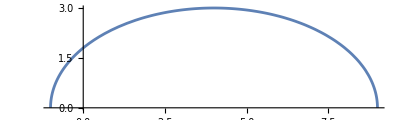

```mathematica
PolarPlot[r[ϕ], {ϕ,0,Pi}, AspectRatio->3/10]
```

This is half of an ellipse, which is why I said this is a “very cool” path — at least Newton would have thought so. What is the length of half of an ellipse? Well, I’ll tell you, in this case it is π √((3^2+5^2)/2)


What is this length numerically (to the nearest 0.1)?



Does it roughly agree with what you got in (d)?



I am very hopeful this problem is starting to get you used to how you compute path lengths using coordinate differences and metrics. You will soon be using very similar techniques to compute elapsed proper time.

## Problem 2 — Set Up the Construction Problem

Your classmates (Sasha and Eden), are going to do the full consultation to the Black Hole Construction Company. The other 6 of you have heard about the consulting project but are only going to do Part A. Please do Part A by making two drawings that show (i) What the President mistakenly had his robots doing, and (ii) what his robots should instead be doing.

If you make your drawings appropriate for building shells from 11,000 meters down to 10,000 meters in 1-meter intervals that would be very hard to draw to scale. Therefore change the problem to be to build shells extending from 15km down to 10km in 1km intervals. That should be drawable to scale. Of course, spacetime is curved and you have flat paper. So you will either have to sacrifice the r scale or the circumferences. Let’s make the circumferences realistic, and sacrifice the r scale. In Part A, you are only being asked to draw one such pair of shells.

More space for lovely drawings.

## Problem 3 — This isn’t a Problem ;)

This is actually just a reminder. I think it is important for people to come in with a serious question about the reading, and that that question be sufficiently well-formulated to have written it down on a piece of paper, like we did in class for Chapter 1.

Could you all do this in advance of class, as if it were homework, and hand it to whomever volunteers to be our  question chair as Eden did for the last class? I’d like to budget 15 minutes (give or take — e.g., 10 to 20 minutes) for discussion and debate about whatever you wish to focus on from EBH (Exploring Black Holes).

Tear off this page, write your name and question on it, and have it ready to hand to your chosen question chair. After the discussion, it will simply be trashed, but it is still a valuable exercise.